```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False]
```

Calculations and notes in Quad 2.4, 25/05/2022 and references therein
Final figures with proper legend and colors etc in “../PhD_thesis/Chapter5/figs_create”
To get back the legends, refer to “graph.nb”

# Fold

Scaling k~Sqrt[p]

### Variance

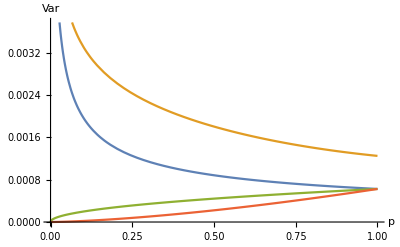

```mathematica
σ=0.05;
t={5};
k0=1;
a=1;
Plot[{(σ^2/(4*Sqrt[p])),((1-Sqrt[p])+Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]*(1/(2*(k0-a*(k0-Sqrt[p])))))*0.05^2,σ^2*Sqrt[p]/4,σ^2*p^(3/2)/4},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotStyle->{Dashed[None],Dashed[None],Dashed[None]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Autocorrelation

A = Cov/Sqrt[Var]
For a stationary process, A = Exp[-Δ k τ]

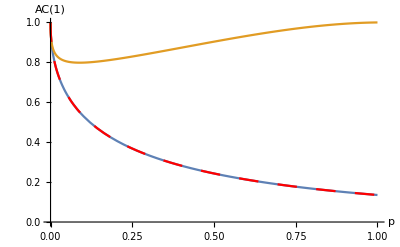

```mathematica
t1=3;
t2=5;
deltat=t2-t1;
k0=1.01;
Plot[{Exp[-2*Sqrt[p]],(Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]/(2*(k0-a*(k0-Sqrt[p])))+(ⅇ^((-2 k0+a (k0-Sqrt[p]))^2/(2 a)) √(π/2) (Erf[(√2 k0)/(√a)]+Erf[(-2 k0+a (k0-Sqrt[p]))/(√2 √a)]))/(√a))/((k0-Sqrt[p])+Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]*(1/(2*(k0-a*(k0-Sqrt[p]))))),Exp[-2*Sqrt[p]]},{p,0,1},AxesLabel->{Style["p",18],Style["AC(1)",18]},PlotStyle->{Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Coefficient Variation

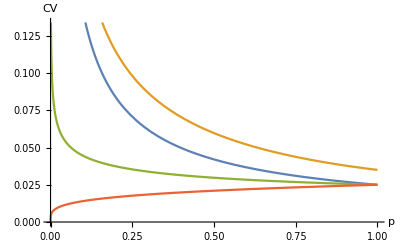

```mathematica
Plot[{σ/(2*p^(3/4)),Sqrt[((1-Sqrt[p])+Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]*(1/(2*(k0-a*(k0-Sqrt[p])))))*0.05^2]/(Sqrt[p]),Sqrt[σ^2/4]/(p^(1/4)),Sqrt[σ^2/4]*(p^(1/4))},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Measurement uncertainties

#### On Variance

Let us imagine we have measurement errors that account for a second σ_2 in addition to the O-U σ. Then the variance is shifted by a term Var+σ_2. Plot below shows the effect of different intrinsic noise levels on the variance ([[1]],[[2]],[[3]]) and of measurement uncertainties [[4]]. As we can see, the measurement uncertainties are less impactful on the leading indicator than the intrinsic noise, especially when approaching the bifurcation.

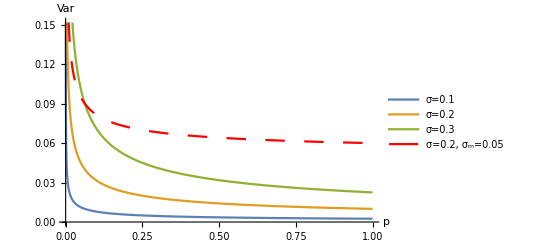

```mathematica
d3={0.1,0.2,0.3};
Plot[{(d3[[1]]^2/(4*Sqrt[p])),(d3[[2]]^2/(4*Sqrt[p])),(d3[[3]]^2/(4*Sqrt[p])),((d3[[2]]^2/(4*Sqrt[p]))+0.05)},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotStyle->{Dashed[None],Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15],PlotLegends->Placed[LineLegend[{"σ=0.1","σ=0.2","σ=0.3","σ=0.2, σ_m=0.05"},LabelStyle->{GrayLevel[0.2],16},LegendLayout->{"Row",2}],{0.55,0.75}]]
```

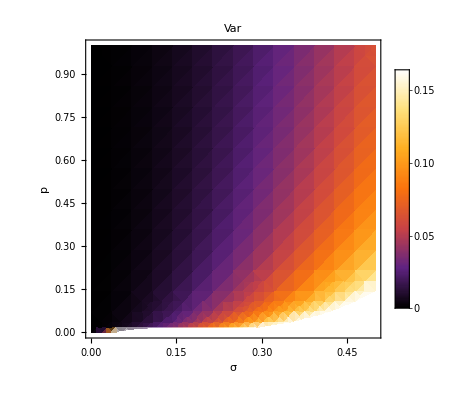

```mathematica
DensityPlot[(sigma^2/(4*Sqrt[p])),{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],PlotLegends->Automatic,FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["Var",FontSize->20],FrameTicksStyle->Directive[Black,18]] (* Original *)
```

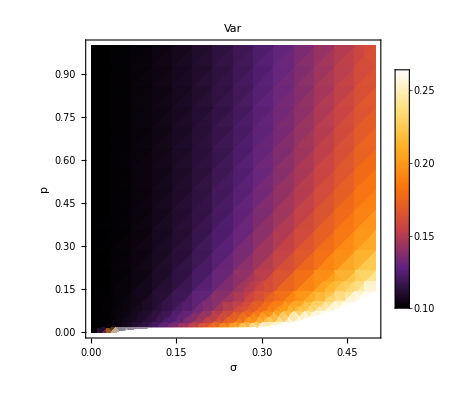

```mathematica
newsigma = 0.1;
DensityPlot[(sigma^2/(4*Sqrt[p])+newsigma),{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],PlotLegends->Automatic,FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["Var",FontSize->20],FrameTicksStyle->Directive[Black,18]] (* With measurement error *)
```

#### On autocorrelation

As for the variance, let us imagine to add some additive uncertainty coming from measurement imperfections. The autocorrelation is impacted by a larger variance that normalize it. See analytical derivation on Quad 2.1, 21/11/19.

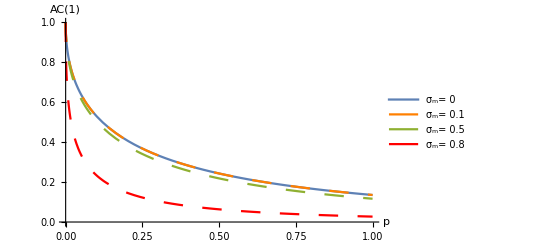

```mathematica
d1=0.5;
sigmaMeas = {0,0.1,0.5,0.8}; (* measurement uncertainty variance *)
Plot[{Exp[-2*Sqrt[p]],
(Exp[-2*Sqrt[p]]*d1^2)/(4*Sqrt[p]*(sigmaMeas[[1]]^2+d1^2/(4*Sqrt[p]))),
(Exp[-2*Sqrt[p]]*d1^2)/(4*Sqrt[p]*(sigmaMeas[[2]]^2+d1^2/(4*Sqrt[p]))),
(Exp[-2*Sqrt[p]]*d1^2)/(4*Sqrt[p]*(sigmaMeas[[3]]^2+d1^2/(4*Sqrt[p])))},{p,0,1},AxesLabel->{Style["p",18],Style["AC(1)",18]},PlotStyle->{Dashed[None],{Dashing[Large],Orange},{Dashing[Large]},{Dashing[Large],Red}},PlotLegends->Placed[LineLegend[{"σ_m= 0","σ_m= 0.1","σ_m= 0.5","σ_m= 0.8"},LabelStyle->{GrayLevel[0.2],16},LegendLayout->{"Row",2}],{0.55,0.75}],LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

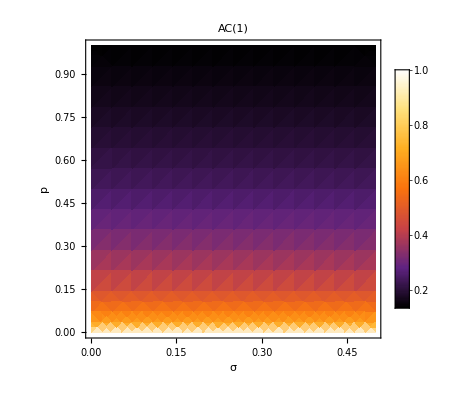

```mathematica
DensityPlot[Exp[-2*Sqrt[p]],{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],PlotLegends->Automatic,FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["AC(1)",FontSize->20],FrameTicksStyle->Directive[Black,18]]
```

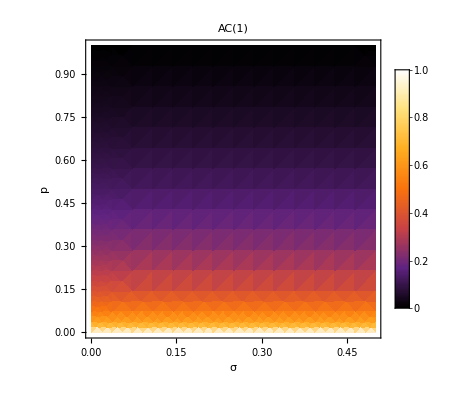

```mathematica
DensityPlot[(Exp[-2*Sqrt[p]]*sigma^2)/(4*Sqrt[p]*(sigmaMeas[[1]]^2+sigma^2/(4*Sqrt[p]))),{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["AC(1)",FontSize->20],FrameTicksStyle->Directive[Black,18],PlotLegends->Placed[BarLegend[{Automatic,{0,1}}],Right]]
```

#### “Realistic” fold

CV where x_mean is capped by some value and does not go until 0 (Quad 2.4, 25/5/22)

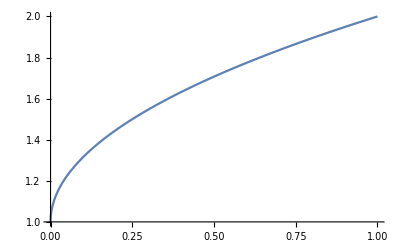

```mathematica
Plot[1+Sqrt[p],{p,0,1}] (* this is the mean *)
```

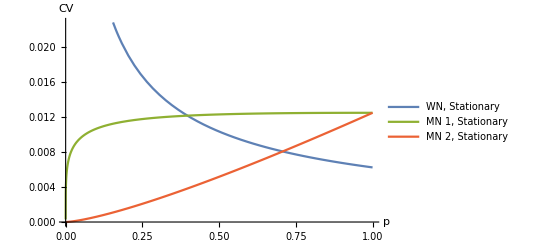

```mathematica
colors=ColorData[97,"ColorList"];
Plot[{σ/(4*p^(1/2))*1/(1+Sqrt[p]),Sqrt[σ^2/4]*p^(1/4)/(1+Sqrt[p]),Sqrt[σ^2/4]*(p^(3/2))/(1+Sqrt[p])},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},PlotStyle->{Dashed[None],{Dashing[None],colors[[3]]},{Dashing[None],colors[[4]]}},PlotLegends->{"WN, Stationary","MN 1, Stationary","MN 2, Stationary"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

```mathematica
colors[[1]]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

RGBColor[0.368417, 0.506779, 0.709798]

# Transcritical

### Variance

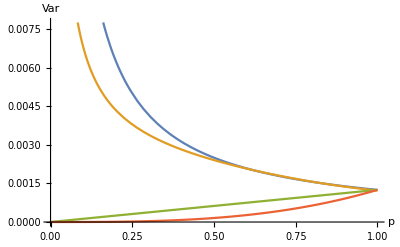

```mathematica
σ=0.05;
σmeas=0.005;
t={5};
Plot[{(σ^2/(2*p)),((1-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p)))))*0.05^2,σ^2*p/2,0.5*σ^2*p^3},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotStyle->{Dashed[None],Dashed[None],Dashed[None]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]] (*MN 1 corresponds to h = sigma x, MN 2 to h = sigma x^2 *)
```

### Autocorrelation

A = Cov/Sqrt[Var]
For a stationary process, A = Exp[-Δ k τ]

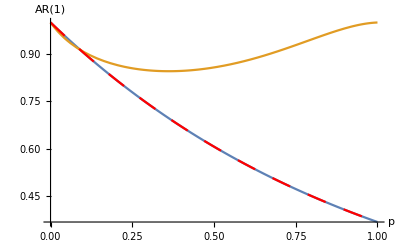

```mathematica
t1=3;
t2=5;
deltat=t2-t1;
k0=1.01;
Plot[{Exp[-p],(Exp[-2*k0*(k0-p)+a*(k0-p)^2]/(2*(k0-a*(k0-p)))+(ⅇ^((k0-a (k0-p))^2/a) √π (Erf[k0/(√a)]+Erf[(-k0+a (k0-p))/(√a)]))/(2 √a))/((k0-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p))))),Exp[-p]},{p,0,1},AxesLabel->{Style["p",18],Style["AR(1)",18]},PlotStyle->{Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Coefficient Variation

doublecheck x_0 > p

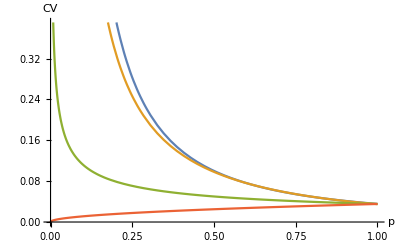

```mathematica
Plot[{σ/(Sqrt[2]*p^(3/2)),Sqrt[((1-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p)))))*0.05^2]/(p),Sqrt[σ^2/(2*p)],Sqrt[p*σ^2/(2)]},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

# Pitchfork

They are the same for subcritical and supercritical (used as a non-critical example)

### Variance

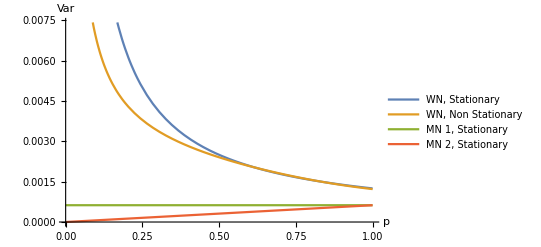

```mathematica
σ=0.05;
t={5};
Plot[{(σ^2/(2*p)),((1-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p)))))*0.05^2,σ^2/4,σ^2*p/4},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotStyle->{Dashed[None],Dashed[None],Dashed[None]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15],PlotLegends->Placed[LineLegend[{"WN, Stationary","WN, Non Stationary","MN 1, Stationary","MN 2, Stationary"},LabelStyle->{GrayLevel[0.2],15},LegendLayout->{"Row",4}],{0.7,0.7}]]
```

### Autocorrelation

A = Cov/Sqrt[Var]
For a stationary process, A = Exp[-Δ k τ]

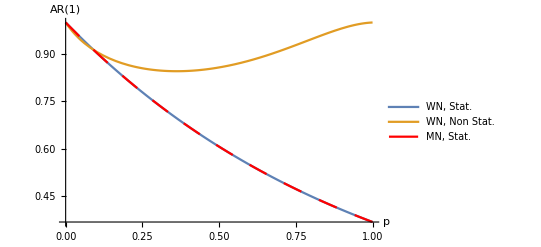

```mathematica
t1=3;
t2=5;
deltat=t2-t1;
k0=1.01;
Plot[{Exp[-p],(Exp[-2*k0*(k0-p)+a*(k0-p)^2]/(2*(k0-a*(k0-p)))+(ⅇ^((k0-a (k0-p))^2/a) √π (Erf[k0/(√a)]+Erf[(-k0+a (k0-p))/(√a)]))/(2 √a))/((k0-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p))))),Exp[-p]},{p,0,1},AxesLabel->{Style["p",18],Style["AR(1)",18]},PlotStyle->{Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15],PlotLegends->Placed[LineLegend[{"WN, Stat.","WN, Non Stat.","MN, Stat."},LabelStyle->{GrayLevel[0.2],15},LegendLayout->{"Row",4}],{0.77,0.55}]]
```

### Coefficient Variation

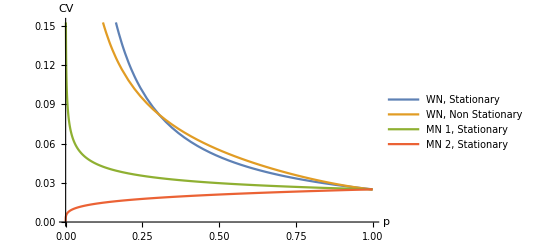

```mathematica
Plot[{σ/(2*p),Sqrt[((1-p)+Exp[-4*k0*(1-p)+a*2*(1-p)^2]/(4*(k0-a*(1-p))))*0.05^2]/Sqrt[p],Sqrt[σ^2/4]/p^(1/4),Sqrt[σ^2/4]*p^(1/4)},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15],PlotLegends->Placed[LineLegend[{"WN, Stationary","WN, Non Stationary","MN 1, Stationary","MN 2, Stationary"},LabelStyle->{GrayLevel[0.2],15},LegendLayout->{"Row",4}],{0.73,0.7}]]
(* CV for x0 ≥ p: ,Sqrt[σ^2/2]*p^(1/4)/(1-p) *)
```

## Spectral reddening

I  do it for a generic k since I saw that substituting k with p only brings a scaling

### Spectral reddening (complete spectrum, k as extra parameter)

“normal” case

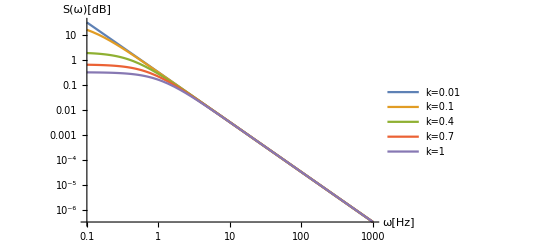

```mathematica
kappa={0.01,0.1,0.4,0.7,1};
sigma1=1;
LogLogPlot[{sigma1^2/(Pi*(kappa[[1]]^2+omega^2)),sigma1^2/(Pi*(kappa[[2]]^2+omega^2)),sigma1^2/(Pi*(kappa[[3]]^2+omega^2)),sigma1^2/(Pi*(kappa[[4]]^2+omega^2)),sigma1^2/(Pi*(kappa[[5]]^2+omega^2))},{omega,0.1,1000},PlotLegends->{"k=0.01","k=0.1","k=0.4","k=0.7","k=1"},AxesLabel->{Style["ω[Hz]",18],Style["S(ω)[dB]",18]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

Multiplicative noise h = sigma x

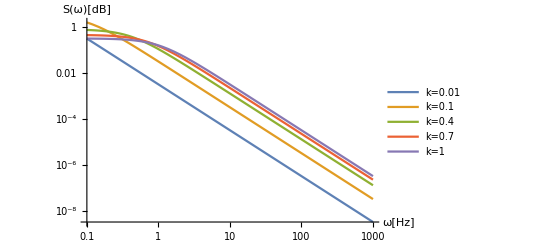

```mathematica
kappa={0.01,0.1,0.4,0.7,1};
sigma1=1;
LogLogPlot[{kappa[[1]]*sigma1^2/(Pi*(kappa[[1]]^2+omega^2)),kappa[[2]]*sigma1^2/(Pi*(kappa[[2]]^2+omega^2)),kappa[[3]]*sigma1^2/(Pi*(kappa[[3]]^2+omega^2)),kappa[[4]]*sigma1^2/(Pi*(kappa[[4]]^2+omega^2)),kappa[[5]]*sigma1^2/(Pi*(kappa[[5]]^2+omega^2))},{omega,0.1,1000},PlotLegends->{"k=0.01","k=0.1","k=0.4","k=0.7","k=1"},AxesLabel->{Style["ω[Hz]",18],Style["S(ω)[dB]",18]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

# Skewness and Kurtosis

Skewness

```mathematica
(*μ=0*)
```

```mathematica
∫_(-∞)^∞ x^3*Exp[-k*x^2/d^2]*Sqrt[k/(Pi*d^2)]ⅆx
```

ConditionalExpression[0, Re[k]>0]

```mathematica
(*μ/=0*)
```

```mathematica
∫_(-∞)^∞ (x-mean)^3*Exp[-k*x^2/d^2]*Sqrt[k/(Pi*d^2)]ⅆx
```

ConditionalExpression[-(mean (3+2 k mean^2))/(2 k), Re[k]>0]

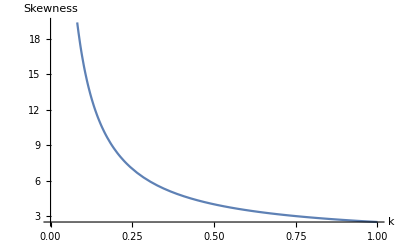

```mathematica
Plot[(3+2* k)/(2 *k),{k,0,1},AxesLabel->{Style["k",18],Style["Skewness",18]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

#### Kurtosis

```mathematica
(* Kurtosis *)
```

```mathematica
∫_(-∞)^∞ (x-mean)^4*Exp[-k*x^2/d^2]*Sqrt[k/(Pi*d^2)]ⅆx
```

ConditionalExpression[(3+4 k mean^2 (3+k mean^2))/(4 k^2), Re[k]>0]